3 - 10 Reduction of order
Reduce to first order and solve, showing each step in detail.

3. y' ' + y'  = 0

Reduction of order is something that Mathematica does not generally need to do.

```mathematica
eqn=y''[x]+y'[x]==0
```

y'[x]+y''[x]==0

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},-ⅇ^-x C[1]+C[2]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

5.  y y' ' = 3 (y')^2

```mathematica
eqn=y[x]y''[x]==3 y'[x]^2
```

y[x] y''[x]==3 y'[x]^2

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},C[2]/(√(2 x+C[1]))]}}

```mathematica
eqn/.sol//Simplify
```

{True}

The text answer is 1/√(c_1 x+c_2). So Mathematica and the text answer each have assigned a value to one of their three constants. This leaves leeway for the remaining assignments to be made in such a way that the two solutions become equivalent.

7.  y' ' +y' ^3Sin[y] = 0

```mathematica
Clear["Global`*"]
```

This problem is a topsy-turvy little trip with an inverted domain. The substitution z=y'[x] is made. Afterwards there is the form

```mathematica
eqn2=z'[y] z[y]==-z[y]^3 Sin[y]
```

z[y] z'[y]==-Sin[y] z[y]^3

Which can be processed by DSolve into the solution

```mathematica
sol2=DSolve[eqn2,z,y]
```

{{z→Function[{y},0]},{z→Function[{y},1/(-C[1]-Cos[y])]}}

The above green cell agrees with the text, though the text uses the inverted form of the fractional expression, calling it ⅆx/ⅆy . Using the terms of the substitution, the solution checks out.

```mathematica
eqn2/.sol2//Simplify
```

{True,True}

The next step is to reverse the substitution level by solving again.

```mathematica
eqn3=-x'[y]==C[1]+Cos[y]
```

-x'[y]==C[1]+Cos[y]

```mathematica
sol3=DSolve[eqn3,x,y]
```

{{x→Function[{y},-y C[1]+C[2]-Sin[y]]}}

The green cell above matches the final answer in the text, with the provision that the sign on the constant -C[1] is opposite to the constant c_1 in the text. The second use of DSolve also checks out true.

```mathematica
eqn3/.sol3
```

{True}

9.  x^2 y' ' -5x y' +9 y = 0, y_1 = x^3

```mathematica
Clear["Global`*"]
```

The substitution y_1 = x^3 works as advertised as a singular solution. If it is ignored,

```mathematica
eqn=x^2 y''[x]-5 x y'[x]+9 y[x]==0
```

9 y[x]-5 x y'[x]+x^2 y''[x]==0

then Mathematica comes up with an equivalent solution, so long as C[1] is assigned the value 0 and C[2] is assigned the value 1/3.

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},x^3 C[1]+3 x^3 C[2] Log[x]]}}

The Mathematica solution, neither more nor less general than the text, checks out.

```mathematica
eqn/.sol//Simplify
```

{True}

11 - 14 Applications of reducible ODEs

11. Curve. Find the curve through the origin in the xy-plane which satisfies y' ' = 2 y' and whose tangent at the origin has slope 1.

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=y''[x]==2y'[x]
```

y''[x]==2 y'[x]

```mathematica
sol=DSolve[{eqn,y'[0]==1,y[0]==0},y,x]
```

{{y→Function[{x},1/2 (-1+ⅇ^(2 x))]}}

The plot below shows that the text answer meets neither of the two requirements stated for the solution. The function in the yellow cell above meets both.

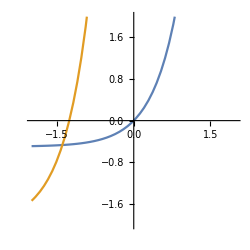

```mathematica
Plot[{1/2 (-1+ⅇ^(2 x)),-2+25 ⅇ^(2 x)},{x,-2,2},AspectRatio->Automatic,PlotRange->{{-2,2},{-2,2}},ImageSize->250]
```

13.  Motion. If, in the motion of a small body on a straight line, the sum of the velocity and acceleration equals a positive constant, how will the distance y[t] depend on the initial velocity and position?

```mathematica
Clear["Global`*"]
```

First, there is an objection against the statement that the sum of velocity and acceleration equals a constant. The two quantities have different units, so they can’t be added. The problem must mean to stipulate that the sum of the coefficients of acceleration and velocity add to a constant. To try to understand this a little bit, I will plot the text answer.

```mathematica
y[t_]=Subscript[c, 1] ⅇ^-t+k t+Subscript[c, 2]
```

k t+ⅇ^-t c_1+c_2

The grid squares do not appear as squares, but the axes’s major ticks seem to be about equal. The problem is supposed to be about travel along a straight line; here the straight line must be the y-axis. With my choice of c_1, c_2, and k = 1 , the starting point must be y = 2, and sum of acceleration and velocity must be 1, and the starting velocity must be 1.

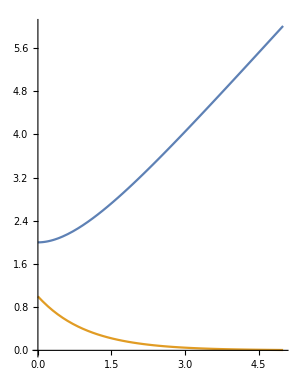

```mathematica
Plot[{ⅇ^-t+t +1,ⅇ^-t},{t,0,5},AspectRatio->1.3,ImageSize->300,GridLines->All]
```

```mathematica
tid=N[Table[{t,ⅇ^-t+t +1},{t,0,15}]]
```

{{0.,2.},{1.,2.36788},{2.,3.13534},{3.,4.04979},{4.,5.01832},{5.,6.00674},{6.,7.00248},{7.,8.00091},{8.,9.00034},{9.,10.0001},{10.,11.},{11.,12.},{12.,13.},{13.,14.},{14.,15.},{15.,16.}}

What can be seen from the two cells below is that by the time t=14, acceleration has nearly disappeared, which means that added velocity is also nearly gone, and the travel velocity is at the rate of the starting velocity.

```mathematica
tir=Table[tid[[n]][[2]]-tid[[n]][[1]],{n,15}]
```

{2.,1.36788,1.13534,1.04979,1.01832,1.00674,1.00248,1.00091,1.00034,1.00012,1.00005,1.00002,1.00001,1.,1.}

```mathematica
N[ⅇ^-14]
```

8.31529×10^-7

```mathematica
y'[t]
```

k-ⅇ^-t c_1

15 - 19 General solution. Initial value problem (IVP)
(More in the next set.) (a) Verify that the given functions are linearly independent and form a basis of solutions of the given ODE. (b) Solve the IVP. Graph or sketch the solution.

15.  4 y'' + 25 y = 0, y[0] = 3.0, y'[0] = -2.5, Cos[2.5 x], Sin[2.5 x]

```mathematica
Clear["Global`*"]
```

By inspection, the two trig expressions are independent. To test whether they are solutions,

```mathematica
eqn=4 y''[x]+25 y[x]==0
```

25 y[x]+4 y''[x]==0

```mathematica
sol=DSolve[{eqn,y[0]==3.0,y'[0]==-2.5},y,x]
```

{{y→Function[{x},3. Cos[(5 x)/2]-1. Sin[(5 x)/2]]}}

The solution checks.

```mathematica
eqn/.sol//Simplify
```

{True}

The two proposed solutions check.

```mathematica
eqn/.Cos[2.5 x]//Simplify
```

ReplaceAll::reps: {Cos[2.5 x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

True/.Cos[2.5 x]

```mathematica
eqn/.Sin[2.5 x]//Simplify
```

ReplaceAll::reps: {Sin[2.5 x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

True/.Sin[2.5 x]

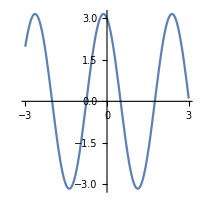

```mathematica
Plot[3. Cos[(5 x)/2]-1. Sin[(5 x)/2],{x,-3,3},AspectRatio->Automatic,ImageSize->200,GridLines->All]
```

17.  4 x^2 y' ' -3 y =0, y(1) = -3, y'(1) = 0, x^(3/2) , x^(-1/2)

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=4 x^2 y''[x]-3 y[x]==0
```

-3 y[x]+4 x^2 y''[x]==0

```mathematica
sol=DSolve[{eqn,y[1]==-3,y'[1]==0},y,x]
```

{{y→Function[{x},-(3 (3+x^2))/(4 √x)]}}

```mathematica
eqn/.sol
```

{True}

Although they look a little different due to their format, the green cell above and the text answer are equivalent.

```mathematica
PossibleZeroQ[-(3 (3+x^2))/(4 √x)-(-0.75 x^(3/2)-2.25 x^(-1/2))]
```

True

Checking the proposed solutions is a little more complicated than usual.

```mathematica
d2=D[x^(3/2),{x,2}]
```

3/(4 √x)

```mathematica
eqn/.{y[x]->x^(3/2),y''[x]->d2}
```

True

```mathematica
d22=D[x^(-1/2),{x,2}]
```

3/(4 x^(5/2))

```mathematica
eqn/.{y[x]->x^(-1/2),y''[x]->d22}
```

True

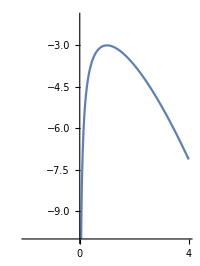

```mathematica
Plot[-(3 (3+x^2))/(4 √x),{x,-2,4},AspectRatio->Automatic,ImageSize->200,GridLines->All,PlotRange->{{-2,4},{-10,-2}}]
```

19.  y'' + 2 y' +2 y = 0, y(0) = 0, y'(0) = 15, ⅇ^-x Cos[x], ⅇ^-x Sin[x]

```mathematica
Clear[eqn,sol]
eqn =y''[x]+2 y'[x]+2 y[x]==0;
sol=DSolve[{eqn,y[0]==0,y'[0]==15},y,x]
```

{{y→Function[{x},15 ⅇ^-x Sin[x]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

```mathematica
f1[x_]=ⅇ^-x Cos[x]
```

ⅇ^-x Cos[x]

```mathematica
d1=D[f1[x],x]
```

-ⅇ^-x Cos[x]-ⅇ^-x Sin[x]

```mathematica
d2=D[f1[x],{x,2}]
```

2 ⅇ^-x Sin[x]

```mathematica
eqn/.{y[x]->f1[x],y'[x]->d1,y''[x]->d2}//Simplify
```

True

```mathematica
f2[x_]=ⅇ^-x Sin[x]
```

ⅇ^-x Sin[x]

```mathematica
d11=D[f2[x],x]
```

ⅇ^-x Cos[x]-ⅇ^-x Sin[x]

```mathematica
d22=D[f2[x],{x,2}]
```

-2 ⅇ^-x Cos[x]

```mathematica
eqn/.{y[x]->f2[x],y'[x]->d11,y''[x]->d22}//Simplify
```

True

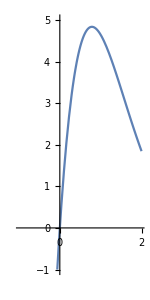

```mathematica
Plot[15 ⅇ^-x Sin[x],{x,-1,2},AspectRatio->Automatic,ImageSize->150,GridLines->All,PlotRange->{{-1,2},{-1,5}}]
```